```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
style1={FontFamily->"Helvetica",16,GrayLevel[0]};
ResourceFunction["AddMatplotlibColors"][]
```

{Magma,Inferno,Plasma,Viridis,EricsRdBuGnYl,EricsRdBuGnYl2,EricsPuBuGnYl,FakeParula,JoesBluGrnPnk2}

## EMT Analysis

This notebook shows the steps for processing the epithelial-to-mesenchymal dataset from van Dijk et al (2018). Data and MATLAB results were from the tutorial:  https://github.com/KrishnaswamyLab/MAGIC and are found in the “data” folder in the same directory as this notebook. Initial processing through graph construction was generally as in Weinreb et al. (2018), except row normalization used the L1 norm and median, as in van Dijk et al., (2018). 

The analyses are compatible with Mathematica 13.3 and were run on an Mac Mini M2 with 32 GB RAM.

### 1. Data import and normalization

• data is imported as an  data matrix (cells x genes) and the median of the row (cell) count totals is defined as the library size for normalization.

```mathematica
emt=Import["data/HMLE_TGFb_day_8_10.csv.gz"];
emt//Dimensions
```

{7524,28910}

```mathematica
emtGenes=emt[[1]];
emtGenes//Short
```

{5S_rRNA,5_8S_rRNA,A1BG,A1BG-AS1,A2M,A2M-AS1,A2ML1,A2ML1-AS1,A4GALT,«28892»,chr22-38_28785274-29006793.1,pk,snoU109,snoU13,snoU2-30,snoU2_19,snoZ196,uc_338,yR211F11.2}

```mathematica
libsize =Total[emt[[2;;,;;]],{2}]//Median
```

4217

• Row normalization is done as in van Dijk et al. (2018), using the L1 norm:

```mathematica
emtNorm=Table[Normalize[emt[[i]]//N,Norm[#,1]&]*libsize,{i,2,7524}]//N;
```

### 2. PCA and graph generation

#### 2a. Dimension reduction by principal components

```mathematica
P1=PrincipalComponents[emtNorm,Method->"Covariance"]; (* unscaled *)
P2=PrincipalComponents[emtNorm,Method->"Correlation"]; (* scaled *)

P1[[1]]//Short
P2[[1]]//Short
```

{5.26849,7.32633,10.9023,21.3325,7.75946,6.83791,8.54491,10.7481,«28894»,0.,0.,0.,0.,0.,0.,0.,0.}

{4.14802,2.34482,1.09085,0.372867,3.30356,2.24311,2.73991,1.16063,«28894»,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
totVar=Normalize[Variance[P1],Total]//Accumulate;totVar[[1;;20]]
```

{0.350737,0.500703,0.564923,0.596435,0.6156,0.630138,0.643068,0.651784,0.660021,0.667964,0.673693,0.678837,0.683906,0.688417,0.692775,0.696515,0.700162,0.703363,0.706263,0.708907}

```mathematica
Max@Select[totVar,#<0.70&]//Position[totVar,#]&
Max@Select[totVar,#<0.85&]//Position[totVar,#]&
```

{{16}}

{{420}}

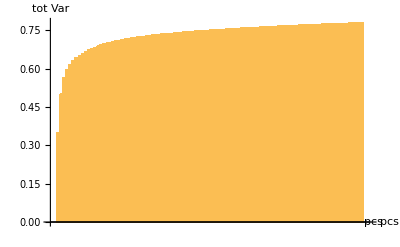

```mathematica
BarChart[totVar[[1;;100]],AxesLabel->{"pcs","tot Var"}]
```

The PrincipalComponents function (“Covariance”) gives the results of SVD on mean zero centered data (unscaled variance), i.e. PC “scores”.

```mathematica
{u,σ,v}=SingularValueDecomposition[Standardize[emtNorm,Mean,1&],200];
```

```mathematica
T=u.σ;
T[[1]]//Short
```

{5.26849,7.32633,10.9023,«195»,-3.59286,1.4829}

PCA is used for dimension reduction; 50 principal components are retained and 10 nearest neighbors used for graph construction to approximate the conditions in the MAGIC tutorial. PCs retained to preserve 70-85% of variance. Nearest neighbors are typically near the square root of the dimensionality, but can be adjusted within a range to give connected graphs that reasonably represent the data.

```mathematica
emtGraph=NearestNeighborGraph[P1[[All,1;;50]],10,VertexCoordinates->Automatic,GraphLayout->"SpringElectricalEmbedding"]//IndexGraph;
```

```mathematica
GraphPlot[emtGraph]
```

-Graphics-

```mathematica
emtCoords=GraphEmbedding[emtGraph,"SpringElectricalEmbedding"];emtCoords//Short
```

{{6.87903,4.74698},«7521»,{4.61862,7.0002}}

```mathematica
VertexCount[emtGraph]
EdgeCount[emtGraph]
```

7523

60670

### 3. Laplacian pseudoinverse and kernel PCA

• return the discrete/combinatorial/unnormalized Laplacian/Kirchhoff matrix of the graph, defined as   , where  is the diagonal matrix of  vertex degrees (degree matrix) and  is the adjacency matrix.

```mathematica
L=KirchhoffMatrix[emtGraph]//N;
Linv=PseudoInverse[L];
```

• Matrix square root of pseudoinverse Laplacian; NOT run -- used for comparison of matrix effectiveness.

```mathematica
Linv2=MatrixPower[Linv,1/2];
```

• testing for significant eigenvalues; SKIP?

```mathematica
{λ,ϕ}=Eigensystem[Linv,60];
```

```mathematica
λ//Short
```

{4.47818,2.77257,2.10991,1.34746,«53»,0.241559,0.241449,0.240579}

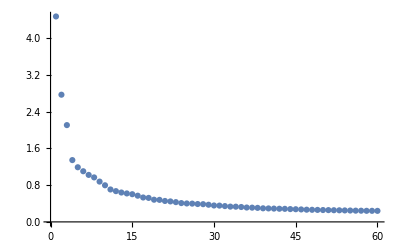

```mathematica
ListPlot[λ,PlotRange->All]
```

The eigendecomposition of the pseudoinverse Laplacian is used to construct the commute time kernel. First, an embedding is made that preserves commute times/resistance distances, using the  square root of the inverse Laplacian eigenvalues (λ). The eigenvalues are ordered in a diagonal matrix (Λ) multiplied by the eigen basis vectors (ϕ). In this notebook, λ is used for the inverse Laplacian values but more generally λ refers to the Laplacian eigenvalues. 

θ = Λ^(1/2)ϕ 	[commute time embedding matrix;  ]   

K_ct= θ^T θ  	[Gram matrix kernel of embedding; commute time kernel] 

K_ct^(1/2)  	[the matrix square root of the commute time kernel is the final kernel form]

```mathematica
{λ,ϕ}=Eigensystem[Linv,30]; 
Λ=ϕ.Linv.Transpose[ϕ];
Θ=(Λ^(1/2)).ϕ;
```

```mathematica
Diagonal[Λ]//Short (* the eigenvalues *)
```

{4.47818,2.77257,2.10991,«24»,0.386231,0.374058,0.357769}

```mathematica
Kct=Transpose[Θ].Θ;
```

```mathematica
Kct2=MatrixPower[Kct,1/2];
```

### 4. Imputation

• Imputation is applied to the full normalized data matrix.

```mathematica
(*LinvImpute=Linv.emtNorm//Re;
Linv2Impute=Linv2.emtNorm//Re;
KImpute=Kct.emtNorm//Re;*)
```

```mathematica
K2Impute=Kct2.emtNorm//Re;
```

#### 4a. scaling imputed gene expression

• scale the imputed expression matrix to the 99th percentile of the original normalized data; linearly transform lowest values to zero. 

,


 

> change for each imputation [ Linv, Linv2, Kct, Kct2 ] if comparisons are needed.

```mathematica
imputeallSc=(Transpose@K2Impute*Map[Quantile[#,0.99]&,Transpose[emtNorm]])/Map[Max[#,10^-8]&,Transpose[K2Impute]]//Transpose;
```

```mathematica
imputeallSc2=Module[{x},(Transpose[imputeallSc]-Min/@Transpose[imputeallSc])*((Max/@Transpose[imputeallSc])-0)/(x=MinMax[#,10^-8]&/@Transpose[imputeallSc];Differences/@x//Flatten)+0//Transpose];
```

```mathematica
LinvImputed=imputeallSc2;
```

```mathematica
Linv2Imputed=imputeallSc2;
```

```mathematica
KImputed=imputeallSc2;
```

```mathematica
K2Imputed=imputeallSc2;
```

#### 4b. magic import from MATLAB

genes from MAGIC: MYC, VIM, FN1, ZEB1, EZH2, SNAIL1, CDH1, CDH2

```mathematica
magicimputed=Import["data/M_imputed.csv"];
```

### 5. Plotting gene expression

#### 5a. color/style parameters

```mathematica
Import["https://pastebin.com/raw/uUJ4rmc1","Package"]
LinearGradientImage[parulaNew,{300,30}];
```

#### 5b. gene interaction plots

```mathematica
posMYC=Position[emtGenes,_?(#=="MYC"&)][[1]][[1]];
posVIM=Position[emtGenes,_?(#=="VIM"&)][[1]][[1]];
posFN=Position[emtGenes,_?(#=="FN1"&)][[1]][[1]];
posZEB=Position[emtGenes,_?(#=="ZEB1"&)][[1]][[1]];
posEZH2=Position[emtGenes,_?(#=="EZH2"&)][[1]][[1]];
posSNAI1=Position[emtGenes,_?(#=="SNAI1"&)][[1]][[1]];
posCDH=Position[emtGenes,_?(#=="CDH1"&)][[1]][[1]];
posCDH2=Position[emtGenes,_?(#=="CDH2"&)][[1]][[1]];
genes2={posMYC,posVIM,posFN,posZEB,posEZH2,posSNAI1,posCDH,posCDH2}//Flatten;
```

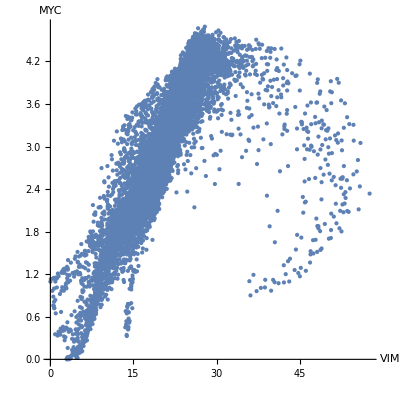

```mathematica
ta1=Transpose[{K2Imputed[[All,posVIM]],K2Imputed[[All,posMYC]]}];
impPlot=Nearest[ta1[[All,{1,2}]]->Rescale[K2Imputed[[All,posZEB]]]];
colfun=parulaNew@First@impPlot[{#1,#2}]&;
ListPlot[ta1,ColorFunction->colfun,ColorFunctionScaling->False,PlotStyle->PointSize[Medium],PlotRange->All,AspectRatio->1,AxesLabel->{"VIM","MYC"},LabelStyle->style1]
```

```mathematica
(*Export["K2_Imp_VIM_MYC.pdf",%]*)
```

L_Imp_VIM_MYC.pdf

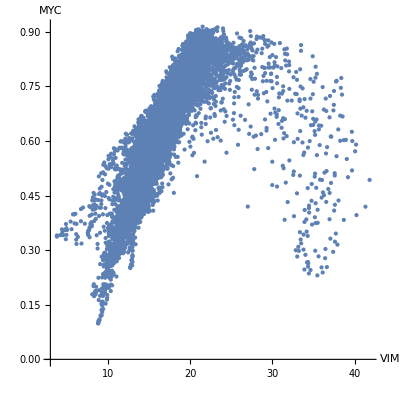

```mathematica
ta2=Transpose[{magicimputed[[All,2]],magicimputed[[All,1]]}];
impPlot=Nearest[ta2[[All,{1,2}]]->Rescale[magicimputed[[All,4]]]];
colfun=parulaNew@First@impPlot[{#1,#2}]&;
ListPlot[ta2,ColorFunction->colfun,ColorFunctionScaling->False,PlotStyle->PointSize[Medium],PlotRange->All,AspectRatio->1,AxesLabel->{"VIM","MYC"},LabelStyle->style1]
```

```mathematica
(*Export["MAG_Imp_VIM_MYC.pdf",%]*)
```

MAG_Imp_VIM_MYC.pdf

#### 5c. more gene expression dynamics

```mathematica
(*posSNA2=Position[emtGenes,_?(#=="SNAI2"&)][[1]][[1]];*)
```

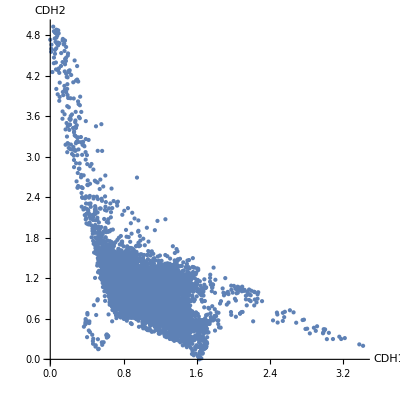

```mathematica
ta11=Transpose[{K2Imputed[[All,posCDH]],K2Imputed[[All,posCDH2]]}];
impPlot=Nearest[ta11[[All,{1,2}]]->Rescale[K2Imputed[[All,posZEB]]]];
colfun=parulaNew@First@impPlot[{#1,#2}]&;
ListPlot[ta11,ColorFunction->colfun,ColorFunctionScaling->False,PlotStyle->PointSize[Medium],PlotRange->All,AspectRatio->1,AxesLabel->{"CDH1","CDH2"},LabelStyle->style1]
```

```mathematica
(*Export["K2_Imp_CDH_CDH2.pdf",%]*)
```

K2_CDH_CDH2.pdf

### 5d. correlation of commute time kernel v. MAGIC imputation

```mathematica
emtGenes[[genes2]]
```

{MYC,VIM,FN1,ZEB1,EZH2,SNAI1,CDH1,CDH2}

```mathematica
CTimputed=K2Impute[[All,genes2]];
```

```mathematica
Table[Correlation[CTimputed[[All,i]],magicimputed[[All,i]]],{i,8}]
%//Mean
```

{0.981122,0.981973,0.97218,0.96182,0.949971,0.956031,0.974323,0.973166}

0.968823

```mathematica
Table[KendallTau[CTimputed[[All,i]],magicimputed[[All,i]]],{i,8}]
%//Mean
```

{0.903569,0.90377,0.853432,0.715707,0.767871,0.727697,0.90527,0.84237}

0.827461

```mathematica
Table[KendallTauTest[CTimputed[[All,i]],magicimputed[[All,i]]],{i,8}]
```

{0.,0.,0.,0.,0.,0.,0.,0.}

### 6. Dropout and down-sample tests

#### 95% dropout

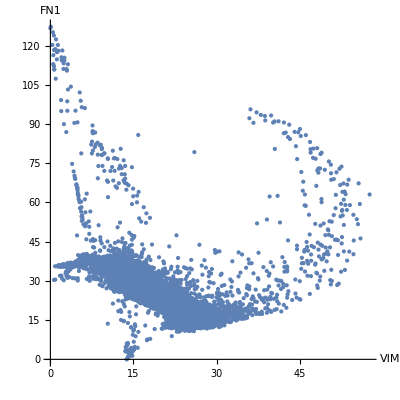

```mathematica
droptest=K2Imputed[[All,genes2 ]];
ta22=Transpose[{droptest[[All,2]],droptest[[All,3]]}];
ListPlot[ta22,PlotStyle->PointSize[Medium],PlotRange->All,AspectRatio->1,AxesLabel->{"VIM","FN1"},LabelStyle->style1]
```

```mathematica
(*Export["FN_predrop.pdf",%];*)
```

```mathematica
SeedRandom[123]; (* change seed for different iterations of the dropout *)
dropout95=droptest*RandomChoice[{5,95}->{1,0},Dimensions[droptest]];
```

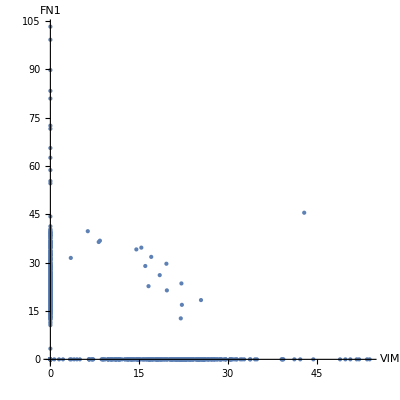

```mathematica
tdrop=Transpose[{dropout95[[All,2]],dropout95[[All,3]]}];
ListPlot[tdrop,PlotStyle->PointSize[Medium],PlotRange->All,AspectRatio->1,AxesLabel->{"VIM","FN1"},LabelStyle->style1]
```

```mathematica
(*Export["FN_95drop.pdf",%];*)
```

reimpute >>

```mathematica
reimpute95=Kct2.dropout95//Re;
(*reimpute98=Kct2.dropout98//Re;*)
```

```mathematica
reimpute95Sc=(Transpose@reimpute95*Map[Quantile[#,0.99]&,Transpose[droptest]])/(Max[#,10^-8]&/@Transpose[reimpute95])//Transpose;
```

```mathematica
reimputed95=Module[{x},(Transpose[reimpute95Sc]-Min/@Transpose[reimpute95Sc])*((Max/@Transpose[reimpute95Sc])-0)/(x=MinMax[#,10^-8]&/@Transpose[reimpute95Sc];Differences/@x//Flatten)+0//Transpose];
```

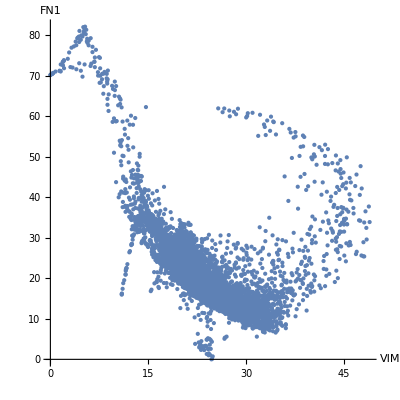

```mathematica
tdrop=Transpose[{reimputed95[[All,2]],reimputed95[[All,3]]}];
ListPlot[tdrop,PlotStyle->PointSize[Medium],PlotRange->All,AspectRatio->1,AxesLabel->{"VIM","FN1"},LabelStyle->style1]
```

```mathematica
(*Export["FN_95_reimp.pdf",%]*)
```

```mathematica
Table[Correlation[reimputed95[[All,i]],droptest[[All,i]]],{i,{2,3}}]
%//Mean
```

{0.919044,0.890548}

0.904796

#### 4 x downsample

```mathematica
Dimensions[emtNorm]
```

{7523,28910}

```mathematica
downSamp=Downsample[emtNorm, {4, 1}];Dimensions[downSamp]
```

{1881,28910}

```mathematica
downRed=DimensionReduce[downSamp,50,Method->"LatentSemanticAnalysis"];
```

```mathematica
downSgraph=NearestNeighborGraph[downRed,10,VertexCoordinates->Automatic,GraphLayout->"SpringElectricalEmbedding"]//IndexGraph;
```

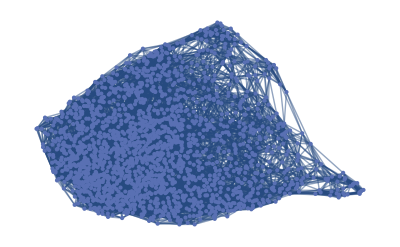

```mathematica
GraphPlot[downSgraph]
```

```mathematica
dsembedd=GraphEmbedding[downSgraph,"SpringElectricalEmbedding"];dsembedd//Short
```

{{6.55825,2.77161},{6.22049,2.73017},«1878»,{3.84599,0.805197}}

```mathematica
L2=KirchhoffMatrix[downSgraph]//N;
L2inv=PseudoInverse[L2];
```

```mathematica
{λ2,U2}=Eigensystem[L2inv,30];Λ2=U2.L2inv.Transpose[U2]//Chop;
𝒮2=(Λ2^(1/2)).U2;𝒮2[[1]]//Short
```

{-0.00551585,-0.00682293,-0.0275848,«1875»,-0.015317,-0.00908192,-0.0185854}

```mathematica
Kpca2=Transpose[𝒮2].𝒮2;
```

```mathematica
sqrKpca2=MatrixPower[Kpca2,1/2];
```

```mathematica
dsimpute=sqrKpca2.downSamp//Re;
```

```mathematica
emtimputeallSc=(Transpose@dsimpute*Map[Quantile[#,0.99]&,Transpose[downSamp]])/Map[Max[#,10^-8]&,Transpose[dsimpute]]//Transpose;
emtimputeallSc//Dimensions
```

{1881,28910}

```mathematica
dsimputed=Module[{x},(Transpose[emtimputeallSc]-Min/@Transpose[emtimputeallSc])*((Max/@Transpose[emtimputeallSc])-0)/(x=MinMax[#,10^-8]&/@Transpose[emtimputeallSc];Differences/@x//Flatten)+0//Transpose];
```

```mathematica
Dimensions[dsimputed]
```

{1881,28910}

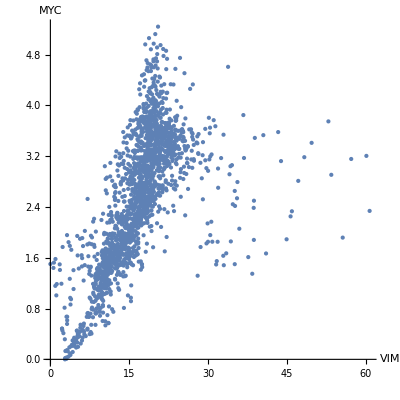

```mathematica
ta33=Transpose[{dsimputed[[All,posVIM]],dsimputed[[All,posMYC]]}];
ListPlot[ta33,PlotStyle->PointSize[Medium],PlotRange->All,AspectRatio->1,AxesLabel->{"VIM","MYC"},LabelStyle->style1]
```

```mathematica
(*Export["MYC_downsamp.pdf",%]*)
```

### 7. Non-linear interaction detection ~ DREMI (OPTIONAL).

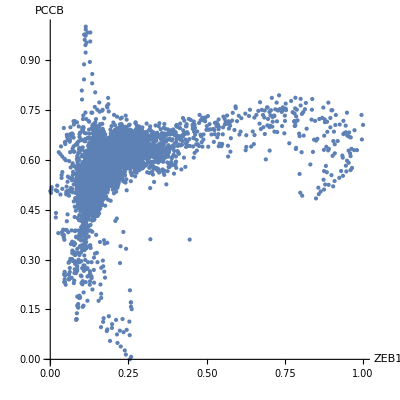

```mathematica
dx=Position[emtGenes,_?(#=="ZEB1"&)][[1]];
dy=Position[emtGenes,_?(#=="PCCB"&)][[1]];
ta4=Transpose[{Rescale@K2Imputed[[All,dx[[1]]]],Rescale@K2Imputed[[All,dy[[1]]]]}];
ListPlot[ta4,Axes->True,PlotStyle->PointSize[Medium],PlotRange->All,AspectRatio->1,AxesLabel->{"ZEB1","PCCB"},LabelStyle->style1]
```

Correlation ()

```mathematica
Correlation[ta4]
```

{{1.,0.360474},{0.360474,1.}}

Kernel density estimation .. . h=bandwidth=0.05 , Gaussian kernel

```mathematica
Dxy=SmoothKernelDistribution[ta4,0.05,"Gaussian"];
Dx=SmoothKernelDistribution[Rescale@K2Imputed[[All,dx[[1]]]],0.05,"Gaussian"];
Dy=SmoothKernelDistribution[Rescale@K2Imputed[[All,dy[[1]]]],0.05,"Gaussian"];
```

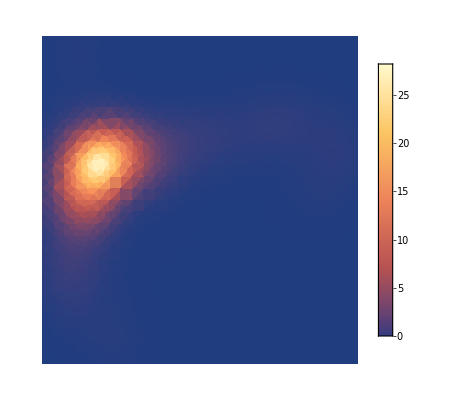

```mathematica
DensityPlot[PDF[Dxy,{xx,yy}],{xx,0,Max[ta4[[All,1]]]},{yy,0,Max[ta4[[All,2]]]},PlotRange->All,Frame->False,PlotLegends->Automatic]
```

Mutual Info (Cover, TM. & Thomas, JA. Elements of information theory):

```mathematica
MI=Quiet@NIntegrate[PDF[Dxy,{xx,yy}]*Log[Max[PDF[Dxy,{xx,yy}],10^-8]/(Max[PDF[Dx,xx],10^-8]Max[PDF[Dy,yy],10^-8])],{xx,-Infinity,Infinity},{yy,-Infinity,Infinity}]
```

0.0777598

Conditional density

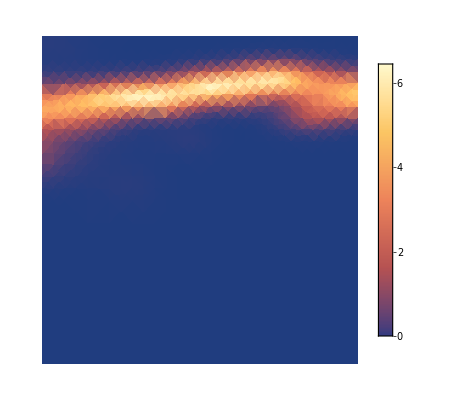

```mathematica
cond=PDF[Dxy,{xx,yy}]/Max[PDF[Dx,xx],10^-8];
DensityPlot[cond,{xx,0,Max[ta4[[All,1]]]},{yy,-1,Max[ta4[[All,2]]]},PlotRange->All,Frame->False,PlotLegends->Automatic]
```

DREMI, Mutual info on conditional density (Krishnaswamy et al., 2014)

```mathematica
DREMI=Quiet@NIntegrate[cond*Log[Max[PDF[Dxy,{xx,yy}],10^-8]/(Max[PDF[Dx,xx],10^-8]Max[PDF[Dy,yy],10^-8])],{xx,-Infinity,Infinity},{yy,-Infinity,Infinity}]
```

1.04692

### 8. M pseudotime matrix

The M matrix is constructed from the symmetrical transition matrix as described in Haghverdi et al. (2016) ;

```mathematica
AdjM=AdjacencyMatrix[emtGraph];
diagM=DiagonalMatrix[VertexDegree[emtGraph]];
T=Inverse[diagM].AdjM//N;
T//Dimensions
```

{7523,7523}

• make the symmetric matrix; test for symmetry --> symmetric if ==Transpose[].
• results are roughly equivalent using   v. T_sym

```mathematica
Subscript[T, sym]=DiagonalMatrix[1/Sqrt[Diagonal[N[Normal[KirchhoffMatrix[emtGraph]]]]]/.ComplexInfinity->0].N[Normal[AdjacencyMatrix[emtGraph]]].DiagonalMatrix[1/Sqrt[Diagonal[N[Normal[KirchhoffMatrix[emtGraph]]]]]/.ComplexInfinity->0];
```

```mathematica
SymmetricMatrixQ/@{T,Subscript[T, sym]}
```

{False,True}

```mathematica
{ev,eb}=Eigensystem[Subscript[T, sym],15];
Short/@{ev,eb}
```

{{1.,0.984351,0.976355,0.969194,«8»,0.897914,0.896637,0.890852},{{-0.00907816,-0.00994463,«7519»,-0.0128385,-0.0107414},«13»,{-0.00546409,«7521»,«21»}}}

Closed form computation of the M matrix (Haghverdi et al., 2016):

 = leading eigenvector

```mathematica
M=Inverse[IdentityMatrix[Length[Subscript[T, sym]]]-(Subscript[T, sym]-(eb[[1]].eb[[1]]))]-IdentityMatrix[Length[Subscript[T, sym]]];
```

```mathematica
MImputed=M.emtNorm//Re;
```

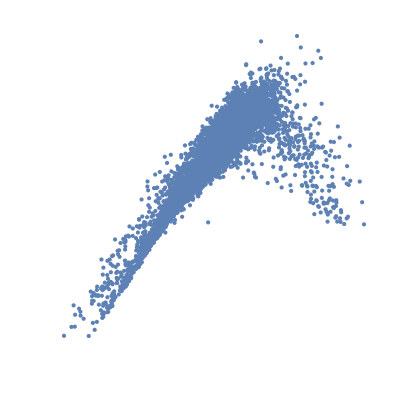

```mathematica
ta3=Transpose[{MImputed[[All,posVIM]],MImputed[[All,posEZH2]]}];
impPlot=Nearest[ta3[[All,{1,2}]]->Rescale[MImputed[[All,posZEB]]]];
colfun=parulaNew@First@impPlot[{#1,#2}]&;
ListPlot[ta3,ColorFunction->colfun,ColorFunctionScaling->False,PlotStyle->PointSize[Medium],PlotRange->All,AspectRatio->1,AxesLabel->{"VIM","MYC"},Axes->False]
```

```mathematica
Table[KendallTau[K2Imputed[[All,i]],MImputed[[All,i]]],{i,genes2[[{1,2,3,4,5,7,8}]]}]
%//Mean
```

{0.850328,0.832865,0.772986,0.752868,0.744118,0.814631,0.841792}

0.80137

```mathematica
Table[Correlation[K2Imputed[[All,i]],MImputed[[All,i]]],{i,genes2[[{1,2,3,4,5,7,8}]]}]
%//Mean
```

{0.951067,0.933674,0.922001,0.931585,0.920828,0.92488,0.93939}

0.931918

```mathematica
Table[Correlation[K2Imputed[[All,i]],MImputed[[All,i]]],{i,genes2[[{1,2,3,4,5,7,8}]]}]
%//Mean
```

{0.951067,0.933674,0.922001,0.931585,0.920828,0.92488,0.93939}

0.931918

```mathematica
M2=MImputed[[All,genes2]];
```

```mathematica
Table[Correlation[M2[[All,i]],magicimputed[[All,i]]],{i,8}]
%//Mean
```

{0.940866,0.901035,0.846097,0.925441,0.873857,0.903951,0.858708,0.896453}

0.893301

### 9. References

Cover, T.M., Thomas, J.A., 1991. Elements of Information Theory. John Wiley and Sons. https://doi.org/10.1002/0471200611

Krishnaswamy, S., Spitzer, M.H., Mingueneau, M., Bendall, S.C., Litvin, O., Stone, E., Pe’er, D., Nolan, G.P., 2014. Systems biology. Conditional density-based analysis of T cell signaling in single-cell data. Sci. (N. York, NY) 346, 1250689. https://doi.org/10.1126/science.1250689

van Dijk, D., Sharma, R., Nainys, J., Yim, K., Kathail, P., Carr, A.J., Burdziak, C., Moon, K.R., Chaffer, C.L., Pattabiraman, D., Bierie, B., Mazutis, L., Wolf, G., Krishnaswamy, S., Pe’er, D., 2018. Recovering Gene Interactions from Single-Cell Data Using Data Diffusion. Cell 174, 716-729.e27. https://doi.org/10.1016/j.cell.2018.05.061

Weinreb, C., Wolock, S., Tusi, B.K., Socolovsky, M., Klein, A.M., 2018. Fundamental limits on dynamic inference from single-cell snapshots. Proceedings of the National Academy of Sciences 115, E2467–E2476. https://doi.org/10.1073/pnas.1714723115

### random graph stuff

```mathematica
randg=RandomGraph[DegreeGraphDistribution[(v=VertexDegree[emtGraph])]];
```

```mathematica
GraphPlot[randg]
```

-Graphics-

```mathematica
Lr=KirchhoffMatrix[randg]//N;
{λr,Ur}=Eigensystem[PseudoInverse@Lr];
λr[[1;;25]]
```

{0.160767,0.159717,0.158966,0.158492,0.157918,0.157841,0.157735,0.157424,0.157322,0.157076,0.156982,0.156604,0.156365,0.156269,0.155923,0.155829,0.155568,0.155514,0.155428,0.15536,0.15515,0.155011,0.154789,0.154656,0.15459}

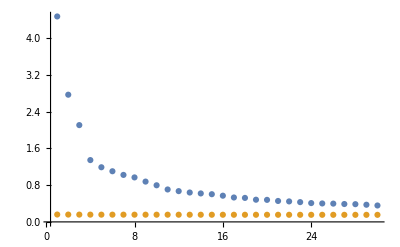

```mathematica
ListPlot[{λ[[1;;30]],λr[[1;;30]]},PlotRange->All]
```

```mathematica
Min@Select[λ,#>0.160&]//Position[λ,#]&
```

{{30}}

```mathematica
DistributionFitTest[λr]
```

0

```mathematica
ℋ=DistributionFitTest[λr,Automatic,"HypothesisTestData"];
```

```mathematica
ℋ["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 35.3522 | 0.
Baringhaus-Henze | 37.6928 | 0.
Cramér-von Mises | 5.46645 | 0.
Jarque-Bera ALM | 250.969 | 0.
Kolmogorov-Smirnov | 0.0447581 | 0.
Kuiper | 0.0697942 | 0.
Mardia Combined | 250.969 | 0.
Mardia Kurtosis | -10.2324 | 1.41932×10^-24
Mardia Skewness | 146.23 | 1.15619×10^-33
Pearson χ^2 | 455.295 | 2.93905×10^-58
Watson U^2 | 4.56466 | 0.

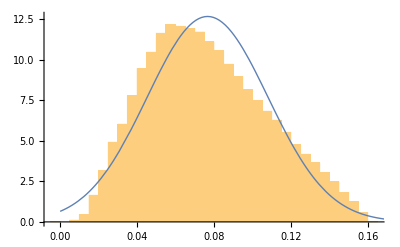

```mathematica
Show[Histogram[λr,Automatic,"ProbabilityDensity"],Plot[PDF[ℋ["FittedDistribution"],x],{x,0,5},PlotStyle->Thick,PlotRange->All]]
```

```mathematica
EstimatedDistribution[λr,WignerSemicircleDistribution[lam,sig]]
```

WignerSemicircleDistribution[0.0803837,0.0803989]

```mathematica
DistributionFitTest[λr,WignerSemicircleDistribution[0.08,0.08]]
```

0.

```mathematica
DistributionFitTest[λ,WignerSemicircleDistribution[0.08,0.08]]
```

0.